```mathematica
eq1=MD-(0.68 bw x fcd (d-0.4 x)+Asl Sigsl(d-dl))
eq2=0.68 bw x fcd+Asl Sigsl-As Sigs
subst={Sigs->2100000 0.00207,Sigsl->2100000 0.01(x-4)/(55-x),Asl->2.45436926,As->2Pi,bw->25,d->55,dl->4,fcd->200/1.4}
Solve[{eq11==0,eq22==0},{MD,x}]
```

MD-Asl (d-dl) Sigsl-0.68 bw fcd (d-0.4 x) x

-As Sigs+Asl Sigsl+0.68 bw fcd x

{Sigs→4347.,Sigsl→(21000. (-4+x))/(55-x),Asl→2.45437,As→2 π,bw→25,d→55,dl→4,fcd→142.857}

```mathematica
eq11=eq1/.subst
eq22=eq2/.subst
```

MD-(2.62863×10^6 (-4+x))/(55-x)-2428.57 (55-0.4 x) x

-27313.+(51541.8 (-4+x))/(55-x)+2428.57 x

```mathematica
Solve[eq22==0,x]
```

{{x→8.96008},{x→78.5095}}

```mathematica
39.87/2
```

19.935

```mathematica
Solve[{eq11==0,eq22==0},{MD,x}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{MD→1.40201×10^6,x→8.96008},{MD→-3.83201×10^6,x→78.5095}}

```mathematica
2 (Pi 1.25^2/4)
2 (Pi 2^2/4)
```

2.45437

2 π

```mathematica
55/(1+(2.07/3.5))
```

34.5601

```mathematica
55/(1+(10/3.5))
```

14.2593

```mathematica
d=50;
Solve[(3.5/d)==3/(d-x),x]
```

{{x→7.14286}}

```mathematica
f=(3.5/x)-2.07/(dd-x);
Solve[f==0,x]
f=(3.5/x)-10/(dd-x);
Solve[f==0,x]
(*DOMINIO 2*)
f=(0/x)-10/(dd-x);
Solve[f==0,x]
f=(3.5/x)-10/(dd-x);
Solve[f==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.628366 dd}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.259259 dd}}

{}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.259259 dd}}

```mathematica
(0.628+0.259)/2
```

0.4435

```mathematica
0.4435 50
```

22.175

```mathematica
55 0.259
```

14.245

```mathematica
eq1=MD-(0.68 bw 0.628 d fcd (d-0.4 0.628 d)+Asl Sigsl(d-dl))
eq2=0.68 bw 0.628 d fcd+Asl Sigsl-As Sigs
subst={Sigs->2100000 es,Sigsl->2100000 0.00207,Asl->2.45436926,As->2Pi,bw->25,dl->4,fcd->200/1.4,MD->2.8 10^6}
Solve[{(eq1==0)/.subst,(eq2==0)/.subst},{es,d}]
```

-0.319768 bw d^2 fcd+MD-Asl (d-dl) Sigsl

0.42704 bw d fcd-As Sigs+Asl Sigsl

{Sigs→2100000 es,Sigsl→4347.,Asl→2.45437,As→2 π,bw→25,dl→4,fcd→142.857,MD→2.8×10^6}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{es→-0.00552338,d→-54.7807},{es→0.00606071,d→45.4384}}

```mathematica
0.628 45
```

28.26

```mathematica
eq1=MD-(0.68 bw 0.628 d fcd (d-0.4 0.628 d)+Asl Young esl(d-dl))
eq2=0.68 bw 0.628 d fcd+Asl Young esl-As Young es
eq3=3.5/(0.628 d)-es/(d-0.628d)
subst={Young->2100000,fcd->200/1.4,bw->25,d->55,MD->4 10^6,dl->4,esl->0.00207}
eq1=eq1/.subst
eq2=eq2/.subst
eq3=eq3/.subst
Solve[{eq1==0,eq2==0,eq3==0},{Asl,As,es}]
```

-0.319768 bw d^2 fcd+MD-Asl (d-dl) esl Young

0.42704 bw d fcd-As es Young+Asl esl Young

5.57325/d-(2.68817 es)/d

{Young→2100000,fcd→142.857,bw→25,d→55,MD→4000000,dl→4,esl→0.00207}

545368.-221697. Asl

83882.9+4347. Asl-2100000 As es

0.101332-0.0488759 es

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Asl→2.45997,As→0.0217226,es→2.07325}}

```mathematica
eq1=MD-(0.68 bw x fcd (d-0.4 x)+Asl Young esl(d-dl))
eq2=0.68 bw x fcd+Asl Young esl-As Young es
eq3=3.5/(x)-es/(d-x)
subst={Young->2100000,fcd->200/1.4,bw->25,d->55,MD->2 10^6,dl->4,esl->0,es->0.00207}
eq1=eq1/.subst
eq2=eq2/.subst
eq3=eq3/.subst
Solve[{eq1==0,eq2==0},{As,x}]
```

MD-0.68 bw fcd (d-0.4 x) x-Asl (d-dl) esl Young

0.68 bw fcd x-As es Young+Asl esl Young

-es/(d-x)+3.5/x

{Young→2100000,fcd→142.857,bw→25,d→55,MD→2000000,dl→4,esl→0,es→0.00207}

2000000-2428.57 (55-0.4 x) x

-4347. As+2428.57 x

-0.00207/(55-x)+3.5/x

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{As→9.5533,x→17.0998},{As→67.2649,x→120.4}}

```mathematica
(2.07/3.5)+1
```

1.59143

0.628931

-(b Q x)/(a+b)

-(b x)/(a+b)

-(a Q (a+b-x))/(a+b)

-(a (a+b-x))/(a+b)

-(a^5 Q)/(3 (a+b)^2)+(a^3 b^2 Q)/(3 (a+b)^2)+(a^2 b^3 Q)/(3 (a+b)^2)

{Q→1,b→2,a→1,l→3}

-(2 x)/3

1/3 (-3+x)

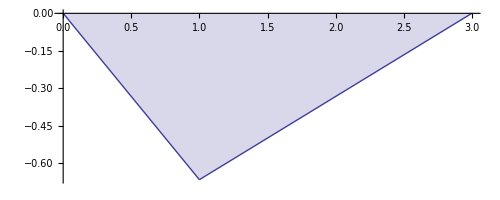

```mathematica
1/1.59
```

```mathematica
TVE
TVE/.subst
```

-(b Q x)/(a+b)

-(b x)/(a+b)

-(a Q (a+b-x))/(a+b)

-(a (a+b-x))/(a+b)

-(a^5 Q)/(3 (a+b)^2)+(a^3 b^2 Q)/(3 (a+b)^2)+(a^2 b^3 Q)/(3 (a+b)^2)

{Q→1,b→2,a→1,l→3}

-(2 x)/3

1/3 (-3+x)

-Graphics-

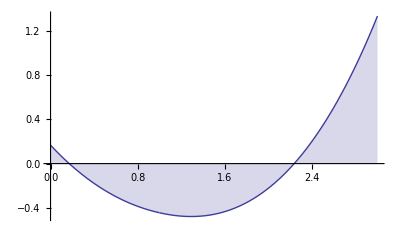

```mathematica
f1R=-Q b x/(a+b)
f1f=- b x/(a+b)
f2R=-(Q a/(a+b))(-x+a+b)
f2f=-( a/(a+b))(-x+a+b)
TVE=Integrate[f1R f1f,{x,0,a}]+Integrate[f2R f2f,{x,a,b}]
subst={Q->1,b->2,a->1,l->3}
f1R=f1R/.subst
f2R=f2R/.subst
p1=Plot[f1R,{x,0,1},Filling->Axis];
p2=Plot[f2R,{x,1,3},Filling->Axis];
Show[p1,p2,PlotRange->All,AxesOrigin->{0,0},AspectRatio->Automatic]
p1=Q b/(6l) (x x x-(l/b) (x-a)^3 -(l l-b b)x);
p2=Q b/(6 l)(x x x - (l l- b b)x);
p11=Plot[p1/.subst,{x,0,1},Filling->Axis];
p22=Plot[p2/.subst,{x,1,3},Filling->Axis];
Show[p11,p22,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
f1R
f2R
```

-(2 x)/3

1/3 (-3+x)

```mathematica
dp=D[p1/.subst,x]
```

1/9 (-5-9/2 (-1+x)^2+3 x^2)

```mathematica
Solve[dp==0,x]//N
```

{{x→1.36701},{x→4.63299}}

```mathematica
7/5.
```

1.4

```mathematica
Table[{x,p1/.subst},{x,1,3,0.1}]
```

{{1.,-0.444444},{1.1,-0.463389},{1.2,-0.476},{1.3,-0.482611},{1.4,-0.483556},{1.5,-0.479167},{1.6,-0.469778},{1.7,-0.455722},{1.8,-0.437333},{1.9,-0.414944},{2.,-0.388889},{2.1,-0.3595},{2.2,-0.327111},{2.3,-0.292056},{2.4,-0.254667},{2.5,-0.215278},{2.6,-0.174222},{2.7,-0.131833},{2.8,-0.0884444},{2.9,-0.0443889},{3.,0.}}